```mathematica
(*REQUIRES MACHINELEARNING FUNCTION*)
```

Defining helper functions to extract column types:

Before looking at structures,  features, pattern, trends, relationships etc. in data, different data types are automatically extracted, to apply appropriate visualization tools

```mathematica
suggestedTypes[d0_,int_Integer:10]:=Module[{info,meta,data},
info=MachineLearning`ToMLDataset@RandomSample[d0,int];
   meta = info[[1, 2, "Input"]];
data=Association@Apply[
#1 -> Append[#2, "Name" -> #1]&,
Transpose[{Keys[meta], Values[info[[2, 1]]]}],
{1}
];
Query[{#Type,#Name,#Values}&]/@Values[data]
]
```

Nominal and textual data type:

```mathematica
conditionalPlot[l0_,conditionText_,method_:"Pie"]:=Module[{pW,pV,hist,label}, (*default values for nominal plot*)
(*if nominal or textual data plot appropriate plots*)
If[MemberQ[l0[[All,1]],conditionText],
pW=Catenate[Position[l0[[All,1]],conditionText]];
Table[
pV=DeleteMissing@l0[[pW[[i]],3]];
Which[ (*using which to avoid different kind of errors*)
AllTrue[AssociationQ[#]&/@pV,TrueQ],
FeatureSpacePlot[Keys[pV]], (*use featurespaceplot for associations*)
AllTrue[((StringContainsQ[ToString[Head[#]],"Entity"])&/@pV),TrueQ],Labeled[WordCloud[pV],Text[l0[[pW[[i]],2]]],Top],
If[AllTrue[NumericQ/@pV,TrueQ],True,pV=DeleteCases[pV,""];Max[WordCount@pV]<=3],
(*if data is good test if wordcloud or histogram/pie plot should be applied*)
Which[ 
DuplicateFreeQ@pV,Nothing,
CountDistinct[pV]<2,Nothing,
CountDistinct[pV]≤20,
	hist=Tally@pV;
	label=hist[[All,1]]//Normal;
	If[method=="Bar",
	BarChart[hist[[All,2]],ChartStyle->RandomChoice[ColorData["Gradients"]],ChartElementFunction->"GlassRectangle",ChartLegends->label,PlotLabel->l0[[pW[[i]],2]]],
	PieChart[hist[[All,2]],ChartStyle->RandomChoice[ColorData["Gradients"]],ChartLegends->label,PlotLabel->l0[[pW[[i]],2]]]
	],
True,Labeled[WordCloud[pV,WordSelectionFunction->(StringLength[#]>1&),FontFamily->RandomChoice[$FontFamilies],ColorFunction->RandomChoice[{"AvocadoColors","DarkRainbow"}],WordOrientation->{{0,π/3}}],Text[l0[[pW[[i]],2]]],Top]
],
True,
Labeled[WordCloud[TextWords@DeleteStopwords@pV,WordSelectionFunction->(StringLength[#]>1&),FontFamily->RandomChoice[$FontFamilies],ColorFunction->RandomChoice[{"DarkRainbow","TemperatureMap","VisibleSpectrum"}]],Text[l0[[pW[[i]],2]]],Top]
],
{i,1,Length[pW]}
]
,Sequence[]]
]
```

Generating Time Series Plot:

```mathematica
timeSeriesPlot[l0_,int_:10]:=Module[{pD,pN,tup,xy,t,ts},
If[MemberQ[l0[[All,1]],"Date"]&&MemberQ[l0[[All,1]],"Numerical"],
pN=Catenate[Position[l0[[All,1]],"Numerical"]];
pD=Catenate[Position[l0[[All,1]],"Date"]];
tup=Tuples[{pD,pN}];
xy=RandomSample[Tuples[{pD,pN}],Min[int,Length[tup]]];
Table[
t=GroupBy[Cases[Thread[l0[[xy[[i]],3]]],x_/;FreeQ[x,_Missing]],First->Last,Total];
Which[
RegularlySampledQ[Keys[t]],
ts=TimeSeries[t,MissingDataMethod->{"Interpolation",InterpolationOrder->1}],
True,
ts=TimeSeries[t,MissingDataMethod->{"Constant",Mean[Values[t]]}]
];
DateListPlot[ts["Path"],Joined->True,Filling->Axis,PlotRange->All,PlotLabel->l0[[xy[[i]],2]][[2]]],
{i,1,Length[xy]}
]
,Sequence[]]
]
```

Plot numerical values in different ways based on dependency test:

```mathematica
numericPlot[l0_,conditionText_,method_:"H",int_Integer:5]:=Module[{pN,pV,pS,v1,v2,pValue,Lab},
If[MemberQ[l0[[All,1]],conditionText],
pN=Catenate[Position[l0[[All,1]],conditionText]];
pV=Replace[#,_?MissingQ->0,{1}]&/@l0[[All,3]];
Which[
Length[pN]≥2,
pS=RandomSample[Subsets[pN,{2}],Min[int,Length[Subsets[pN,{2}]]]];
Table[
v1=pV[[pS[[i]]]][[1]];
v2=pV[[pS[[i]]]][[2]];
If[(Variance[v1]>0&&Variance[v2]>0),
pValue=IndependenceTest[N@v1,N@v2];
Lab="Dependence of " <> ToString[l0[[pS⟦i⟧]][[2]][[2]]]<>" and "<>ToString[l0[[pS[[i]]]][[1]][[2]]];
If[
pValue<0.05,
ListPlot[Transpose[{Normalize[v1],Normalize[v2]}],PlotLegends->Automatic,PlotStyle->Directive[PointSize[Medium],RandomChoice[{Pink,Purple,Black,Green}]],AxesLabel->{l0[[pS⟦i⟧]][[1]][[2]],l0[[pS[[i]]]][[2]][[2]]},PlotTheme->"Monochrome"],
StackedListPlot[{Normalize[v2],Normalize[v1]},AxesLabel->{l0[[pS⟦i⟧]][[1]][[2]],l0[[pS[[i]]]][[2]][[2]]},PlotStyle->PointSize[Medium]]]],
{i,1,Length[pS]}
],
True,
If[method=="H",Histogram[pV[[pN]],PlotLabel->First@l0[[pN,2]],ChartElementFunction->ChartElementDataFunction["SegmentScaleRectangle","Segments"->3,"ColorScheme"->"SolarColors"]],
StackedListPlot[pV[[pN]],PlotLabel->First@l0[[pN,2]],PlotTheme->"Scientific"]
,Sequence[]]]
]
]
```

Detect data types location and apply GeoHistogram:

```mathematica
(*geo plot*)
```

```mathematica
geoPlot[l0_]:=Module[{pL},
If[MemberQ[l0[[All,1]],"Location"],
pL=Pick[l0,StringMatchQ[l0[[All,1]],"Location"]];
Table[
GeoHistogram[pL[[i,3]]]
,{i,1,Length[pL]}]
,Sequence[]]
]
```

Same is done for audios and images:

```mathematica
(*audio plot*)
```

```mathematica
audioPlot[l0_]:=Module[{pA,entry},
If[MemberQ[l0[[All,1]],"Audio"],
pA=Pick[l0,StringMatchQ[l0[[All,1]],"Audio"]];
Table[
entry=RandomChoice[pA[[i,3]]];
Periodogram[entry,1000,PlotLabel->l0[[pA[[i]]]][[2]]],
{i,1,Length[pA]}]
,Sequence[]]
]
(*image plot*)
imagePlot[l0_,int_Integer:10]:=Module[{pI,rI},
If[MemberQ[l0[[All,1]],"Image"],
pI=Pick[l0,StringMatchQ[l0[[All,1]],"Image"]];
Table[
rI=RandomSample[pI[[i,3]]];
FeatureSpacePlot[rI,Min[int,Length[rI]]],
{i,1,Length[pI]}
]
,Sequence[]]
]
```

Entities have to be treated differently as they have a whole bunch of properties and therefore for each entity column a data set with random property columns is created and again feeding the suggestedColumns function where different data types get extracted.

```mathematica
getEntTable[pE_,int_Integer:10]:=Module[{entities,PropEnt,nE,nP,rP,d,finalD},
Table[
entities=RandomSample[pE[[i]],Min[10,Length[pE[[i]]]]];
nE=EntityTypeName/@entities;
If[AllTrue[nE,MemberQ[EntityValue[],#]&],
nP=Entity[First@nE]["Properties"];
rP=RandomSample[nP,Min[int,Length[nP]]];
PropEnt=EntityValue[entities,rP];
d=Dataset[Association[Thread[Prepend[CommonName[rP],First@nE]->#]]&/@Transpose[Join[{CommonName[entities]},Transpose@PropEnt]]];
finalD=d[{Identity,Merge[Identity]/*Select[Count[#,_Missing]/Length[#]>0.01&]/*Keys}/*Apply[KeyDrop]];
suggestedTypes[finalD,10]
],{i,1,Length[pE]}]
]
```

```mathematica
(*Main Function which generates all Plots*)
MainFunction[d0_,intP_:10,nomP_:"H",numP_:"H",intN_:10,intI_:10,intE_:10,intT_:10]:=Module[{posT,pE,d,entTab,PlotNom,PlotText,PlotNumeric,PlotImage,PlotTime,PlotAudio,PlotGeo,PlotNomE=Sequence[],PlotTextE=Sequence[],PlotNumericE=Sequence[],PlotImageE=Sequence[],PlotTimeE=Sequence[],PlotAudioE=Sequence[],PlotGeoE=Sequence[],return}, (*put in dataobject, may adjust*)
Which[
d0["ContentTypes"]=={"Entity Store"},Nothing,
d0["ContentTypes"]=={"Text"},
Labeled[WordCloud[TextWords@DeleteStopwords@StringDelete[RandomSample[ResourceData[d0],intP],{DigitCharacter..,PunctuationCharacter..}]],Text["Written Text"],Top],
d0["ContentTypes"]=={"Image"},
FeatureSpacePlot[Keys[RandomSample[ResourceData[d0],intP]]],
True,
d=ResourceData[d0]/.{IntegerPart[__]->Missing[],""->Missing[]};
posT=Select[suggestedTypes[d,intP],FreeQ[Hyperlink]];
PlotNom=conditionalPlot[posT,"Nominal",nomP];
PlotText=conditionalPlot[posT,"Text",nomP];
PlotNumeric=numericPlot[posT,"Numerical","H",intN]; 
PlotImage=imagePlot[posT,intI];
PlotGeo=geoPlot[posT];
PlotTime=timeSeriesPlot[posT,intT];
PlotAudio=audioPlot[posT]; (*maybe here too just to be sure*)
If[MemberQ[posT[[All,1]],"Entity"],
pE=DeleteCases[#,_Missing]&/@Pick[posT[[All,3]],StringMatchQ[posT[[All,1]],"Entity"]];
entTab=getEntTable[pE,intE];(*may add treshhold here for missings*)
Table[
PlotNomE=conditionalPlot[entTab[[i]],"Nominal",nomP];
PlotTextE=conditionalPlot[entTab[[i]],"Text",nomP];
PlotNumericE=numericPlot[entTab[[i]],"Numerical","H",intN]; 
PlotImageE=imagePlot[entTab[[i]],intI];
PlotTimeE=timeSeriesPlot[entTab[[i]],intT]; 
PlotAudioE=audioPlot[entTab[[i]]]; (*maybe here too just to be sure*)
PlotGeoE=geoPlot[entTab[[i]]] (*adapt that too, if time*)
,{i,1,Length[entTab]}
],Sequence[]
];
return=Flatten[{PlotNom,PlotText,PlotNumeric,PlotGeo,PlotTime,PlotAudio,PlotImage,PlotNomE,PlotTextE,PlotNumericE,PlotImageE,PlotTimeE,PlotAudioE,PlotGeoE}]
]
]
```

```mathematica
res=MainFunction[ResourceObject["Mass Shootings in America"],60];
```

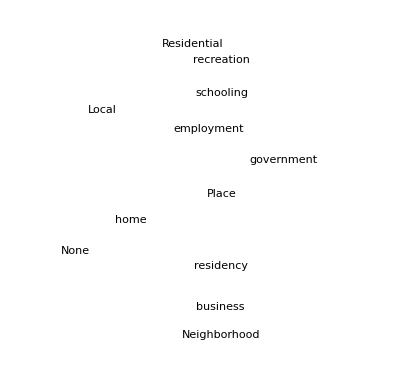
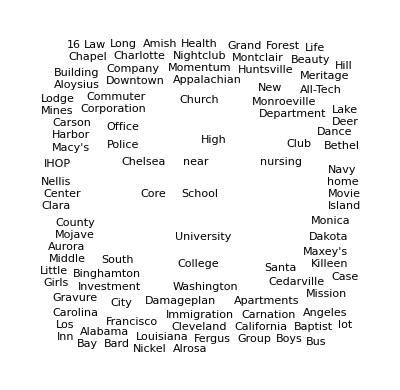
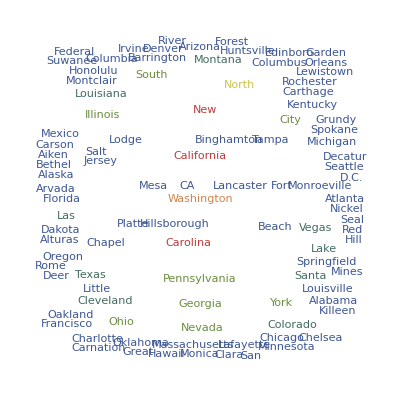
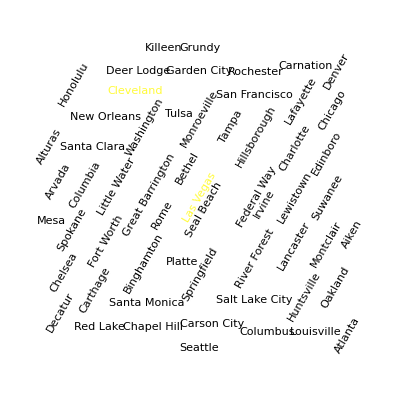
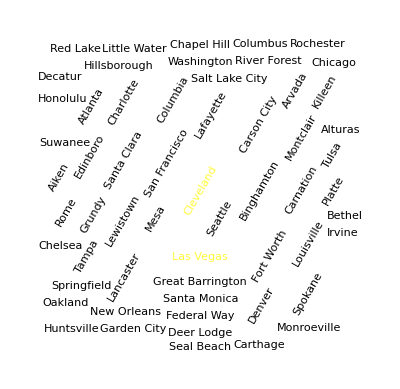
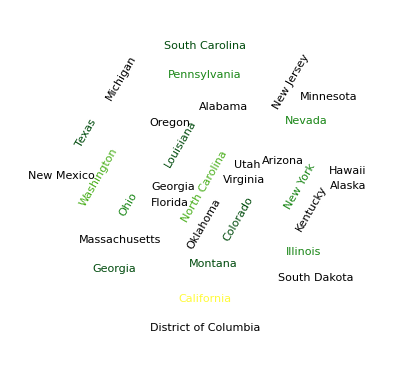
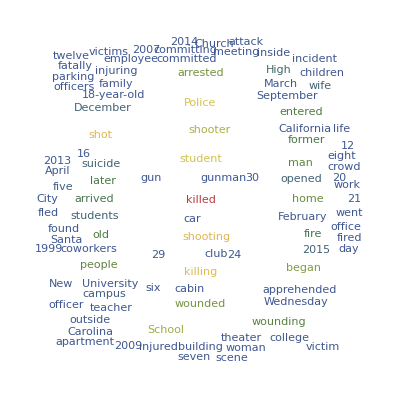
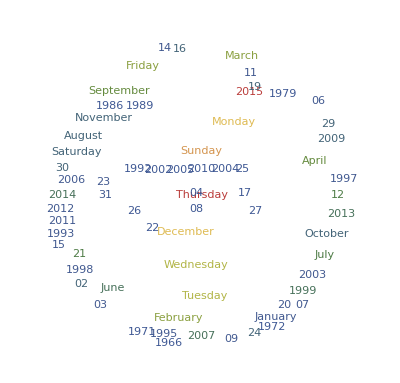
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-Relationship to Incident Location,-Graphics-,-Graphics-,-Graphics-,-Graphics-Title,-Graphics-Location,-Graphics-City,-Graphics-City/Geo,-Graphics-State,-Graphics-Description,-Graphics-Date - Detailed,-Graphics-Shooter Race,-Graphics-Place Type,-Graphics-Targeted Victim/s -Detailed,-Graphics-Targeted Victim/s-General,-Graphics-Possible Motive -  Detailed,-Graphics-,-Graphics-History of Mental Illness - Detailed,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,Null}

```mathematica
res
```